## The bond impurity problem in triangular lattice heisenberg AFM

### Structure factor

```mathematica
e1={1,0};
e2={-1/2,(√3)/2};
e3={-1/2,(-√3)/2};
```

```mathematica
Simplify[1/6(2(Cos[k.e1]+Cos[k.e2]+Cos[k.e3]))]
```

1/3 (Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])

```mathematica
gamma[kx_,ky_]:=1/3 (Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])
```

### Single bond impurity

```mathematica
k={kx,ky}
```

{kx,ky}

```mathematica
ExpToTrig[Exp[I k.e1]]
```

Cos[kx]+ⅈ Sin[kx]

```mathematica
FullSimplify[Cos[kx]+ⅈ Sin[kx]]
```

ⅇ^(ⅈ kx)

```mathematica
alpha[kx_,ky_]:=1-(Cos[kx]+I Sin[kx] )
```

```mathematica
FullSimplify[Series[alpha[q Cos[θ],q Sin[θ]]/(gamma[q Cos[θ],q Sin[θ]]-1),{q,0,2}]]
```

(4 ⅈ Cos[θ])/q-2 Cos[θ]^2-1/12 ⅈ (3 Cos[θ]+2 Cos[3 θ]) q+1/48 (Cos[2 θ]+Cos[4 θ]) q^2+O[q]^3

```mathematica
FullSimplify[Series[alpha[(4π)/3+q Cos[θ],q Sin[θ]]/(gamma[(4π)/3+q Cos[θ],q Sin[θ]]-1),{q,0,2}]]
```

(-1-ⅈ/(√3))+1/3 (-ⅈ+√3) Cos[θ] q+1/36 (2 ⅈ √3+(3+3 ⅈ √3) Cos[2 θ]) q^2+O[q]^3

```mathematica
FullSimplify[Series[alpha[-(4π)/3+q Cos[θ],q Sin[θ]]/(gamma[-(4π)/3+q Cos[θ],q Sin[θ]]-1),{q,0,2}]]
```

(-1+ⅈ/(√3))-1/3 ((ⅈ+√3) Cos[θ]) q+1/36 (-2 ⅈ √3+(3-3 ⅈ √3) Cos[2 θ]) q^2+O[q]^3

### Response function and correlatation function calculation

```mathematica
Integrate[Exp[I K Cos[x]],{x,0,2π}]
```

ConditionalExpression[2 π BesselJ[0,Abs[K]],K∈Reals]

```mathematica
Limit[BesselJ[0,K],K-> ∞]
```

0

```mathematica
FullSimplify[Integrate[x((Cos[y](x Cos[y]-r))/(x(r^2+x^2-2r x Cos[y]))-Cos[y]^2/x^2),{y,0,2π}]]
```

-(π (r^2+x^2) (r+x+r √((r+x)^2/(r-x)^2)-x √((r+x)^2/(-r+x)^2)))/(2 r^2 x (r+x))

```mathematica
FullSimplify[Integrate[-(π (r^2+x^2) (r+x+r √((r+x)^2/(r-x)^2)-x √((r+x)^2/(-r+x)^2)))/(2 r^2 x (r+x)),x]]
```

-(π (r+x+r √((r+x)^2/(r-x)^2)-x √((r+x)^2/(-r+x)^2)) (x^2+2 r^2 Log[x]))/(4 r^2 (r+x))

```mathematica
F[r_,x_]:=-(π (r+x+r √((r+x)^2/(r-x)^2)-x √((r+x)^2/(-r+x)^2)) (x^2+2 r^2 Log[x]))/(4 r^2 (r+x))
```

```mathematica
FullSimplify[F[r,L]-F[r,1]]
```

(π (1+√((1+r)^2/(-1+r)^2)-(2 √((1+r)^2/(-1+r)^2))/(1+r)-((L+r-L √((L+r)^2/(L-r)^2)+r √((L+r)^2/(-L+r)^2)) (L^2+2 r^2 Log[L]))/(L+r)))/(4 r^2)

```mathematica
Corr[r_]:=(π (1+√((1+r)^2/(-1+r)^2)-(2 √((1+r)^2/(-1+r)^2))/(1+r)-((L+r-L √((L+r)^2/(L-r)^2)+r √((L+r)^2/(-L+r)^2)) (L^2+2 r^2 Log[L]))/(L+r)))/(4 r^2)
```

```mathematica
Series[Corr[1/x],{x,0,2}]
```

-π Log[L]+1/2 (π-L^2 π) x^2+O[x]^3

```mathematica
Integrate[Cos[y]^2/x^2,{y,0,2π}]
```

π/x^2

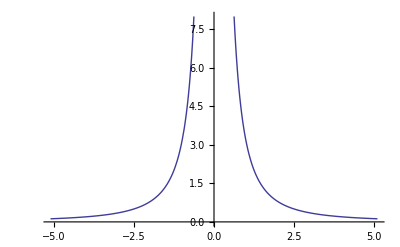

```mathematica
Plot[π/x^2,{x,-5.1,5.1},PlotRange->{0,8}]
```

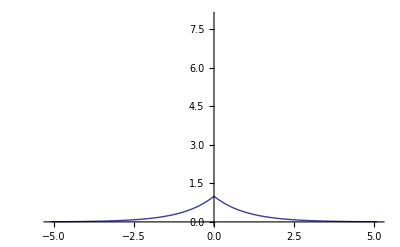

```mathematica
Plot[Exp[-Abs[x]],{x,-5.1,5.1},PlotRange->{0,8}]
```

### Bond impurity between three of the neighbouring six spins which share the same sublattice index

```mathematica
k={kx,ky}
```

{kx,ky}

```mathematica
FullSimplify[ExpToTrig[Exp[I k.e1]+Exp[I k.e2]+Exp[I k.e3]]]
```

ⅇ^(ⅈ kx)+2 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2]

```mathematica
beta[kx_,ky_]:=1-(ⅇ^(ⅈ kx)+2 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2])
```

```mathematica
FullSimplify[Series[beta[q Cos[θ],q Sin[θ]]/(gamma[q Cos[θ],q Sin[θ]]-1),{q,0,2}]]
```

8/q^2-5/2-1/2 ⅈ Cos[3 θ] q+((25-2 Cos[6 θ]) q^2)/1440+O[q]^3

```mathematica
FullSimplify[Series[beta[(4π)/3+q Cos[θ],q Sin[θ]]/(gamma[(4π)/3+q Cos[θ],q Sin[θ]]-1),{q,0,2}]]
```

(-2/3-2 (-1)^(1/3))+1/18 (2+3 ⅈ √3) q^2+O[q]^3

```mathematica
FullSimplify[Series[beta[-(4π)/3+q Cos[θ],q Sin[θ]]/(gamma[-(4π)/3+q Cos[θ],q Sin[θ]]-1),{q,0,2}]]
```

(-2/3+2 (-1)^(2/3))+1/18 (2-3 ⅈ √3) q^2+O[q]^3